Parameters

9.48252×10^42

18000000000

π/9000000000

ⅈ

1.05457×10^-34

H0

{{2.2146×10^-24,0.,0.,0.,0.,0.,0.,0.},{0.,3.16372×10^-25,0.,0.,0.,0.,0.,0.},{0.,0.,-9.49115×10^-25,0.,0.,0.,0.,0.},{0.,0.,0.,-1.58186×10^-24,0.,0.,0.,0.},{0.,0.,0.,0.,-1.58186×10^-24,0.,0.,0.},{0.,0.,0.,0.,0.,-9.49115×10^-25,0.,0.},{0.,0.,0.,0.,0.,0.,3.16372×10^-25,0.},{0.,0.,0.,0.,0.,0.,0.,2.2146×10^-24}}

Jplus and Jminus matrices

SparseArray[…]

SparseArray[…]

H1

SparseArray[…]

Add hamiltonians

{{2.2146×10^-24,0.+1.×10^9 (0.+2.79013×10^-34 ⅇ^(-18000000000 ⅈ t)),0.,0.,0.,0.,0.,0.},{0.+2.79013×10^-25 ⅇ^(18000000000 ⅈ t),3.16372×10^-25,0.+1.×10^9 (0.+3.65314×10^-34 ⅇ^(-18000000000 ⅈ t)),0.,0.,0.,0.,0.},{0.,0.+3.65314×10^-25 ⅇ^(18000000000 ⅈ t),-9.49115×10^-25,0.+1.×10^9 (0.+4.08434×10^-34 ⅇ^(-18000000000 ⅈ t)),0.,0.,0.,0.},{0.,0.,0.+4.08434×10^-25 ⅇ^(18000000000 ⅈ t),-1.58186×10^-24,0.+1.×10^9 (0.+4.21829×10^-34 ⅇ^(-18000000000 ⅈ t)),0.,0.,0.},{0.,0.,0.,0.+4.21829×10^-25 ⅇ^(18000000000 ⅈ t),-1.58186×10^-24,0.+1.×10^9 (0.+4.08434×10^-34 ⅇ^(-18000000000 ⅈ t)),0.,0.},{0.,0.,0.,0.,0.+4.08434×10^-25 ⅇ^(18000000000 ⅈ t),-9.49115×10^-25,0.+1.×10^9 (0.+3.65314×10^-34 ⅇ^(-18000000000 ⅈ t)),0.},{0.,0.,0.,0.,0.,0.+3.65314×10^-25 ⅇ^(18000000000 ⅈ t),3.16372×10^-25,0.+1.×10^9 (0.+2.79013×10^-34 ⅇ^(-18000000000 ⅈ t))},{0.,0.,0.,0.,0.,0.,0.+2.79013×10^-25 ⅇ^(18000000000 ⅈ t),2.2146×10^-24}}

Initial and final states

{1,0,0,0,0,0,0,0}

{0,1,0,0,0,0,0,0}

TDSE numerical solution

{{y→InterpolatingFunction[…]}}

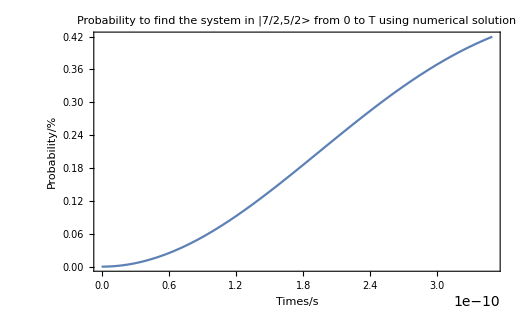

```mathematica
"Parameters"
B=9.482521562467288*10^42
w=18*10^9
T=2Pi/w
i=Sqrt[-1]
hbar=1.0545718176461565*10^-34

Clear[t]

"H0"
Hzero=B*hbar^2*DiagonalMatrix[{21,3,-9,-15,-15,-9,3,21}]

"Jplus and Jminus matrices"
Jp=hbar*({{0, √7, 0, 0, 0, 0, 0, 0}, {0, 0, 2 √3, 0, 0, 0, 0, 0}, {0, 0, 0, √15, 0, 0, 0, 0}, {0, 0, 0, 0, 4, 0, 0, 0}, {0, 0, 0, 0, 0, √15, 0, 0}, {0, 0, 0, 0, 0, 0, 2 √3, 0}, {0, 0, 0, 0, 0, 0, 0, √7}, {0, 0, 0, 0, 0, 0, 0, 0}})
Jm=Transpose[Jp]

"H1"
Hone=B*hbar*(Exp[-i*w*t]*Jp+Exp[i*w*t]*Jm)

"Add hamiltonians"
H=Hzero+Hone

"Initial and final states"
init={1,0,0,0,0,0,0,0}
final={0,1,0,0,0,0,0,0}

"TDSE numerical solution"
state=NDSolve[{i*hbar*(y')[t]-H.y[t]==0, y[0]==init},y,{t,0,T}]
Plot[Evaluate[{Norm[y[t].final]^2}/.state],{t,0,T},PlotRange->Automatic,
 PlotLabel->"Probability to find the system in |7/2,5/2> from 0 to T using numerical solution",
Frame->True,
FrameLabel->{"Times/s","Probability/%"}
]
```